Quantum Case

```mathematica
ClearAll[ω0]
```

```mathematica
a=1/σF^2-ⅈ (B2+B3);
aprime=1/σF^2-ⅈ (B1+B3)-1/(4a)(1/σF^2-2ⅈ B3)^2;
bprime=-ⅈ (A1-A3+τ2+τ3-2/(4a)(1/σF^2-2ⅈ B3) (A2-A3+τ3));
cprime=1/(4a)(A2-A3+τ3)^2+ⅈ ω0/3 (2τ2+τ3);
cnprime=cn ((2π ℏ ωF)/V)^(3/2) ⅇ^(ⅈ (Kf1+Kf2+Kf3-ω0 t))√(π^2/(a aprime));
```

```mathematica
FullSimplify[cnprime*Conjugate[cnprime],Element[ω0|A1|A2|A3|B1|B2|B3|τ2|τ3|σF|ωF|ℏ|Kf1|Kf2|Kf3|ω0|t,Reals]]
```

(32 cn π^5 σF^4 Abs[ωF ℏ]^3 Conjugate[cn])/Abs[V^3 (3-4 ⅈ (B1+B2+B3) σF^2-4 (B2 B3+B1 (B2+B3)) σF^4)]

```mathematica
FullSimplify[Expand[(bprime^2-4aprime cprime)*Conjugate[aprime]+Conjugate[bprime^2-4aprime cprime]*aprime],Element[ω0|A1|A2|A3|B1|B2|B3|τ2|τ3|σF,Reals]]/FullSimplify[Expand[4aprime Conjugate[aprime]],Element[ω0|A1|A2|A3|B1|B2|B3|τ2|τ3|σF,Reals]]
```

((4 σF^4+4 (B2+B3)^2 σF^8) (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 τ2+4 A3 B1 B2 σF^4 τ2+8 A3 B2^2 σF^4 τ2-4 A3 B1 B3 σF^4 τ2+4 A3 B2 B3 σF^4 τ2-3 τ2^2-4 B2^2 σF^4 τ2^2-4 B2 B3 σF^4 τ2^2-4 B3^2 σF^4 τ2^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) τ2) τ3-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ3^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 τ2-τ3)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 τ2-B2 (B1+B3) τ3-2 B2^2 (τ2+τ3)+B3 (-2 B3 τ2+B1 τ3)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (τ2-τ3)+4 σF^4 (-2 B1^2 τ3+B3 (2 B3 τ2+B2 (τ2+τ3))-B1 (B3 (-τ2+τ3)+B2 (τ2+τ3))))))/((2 σF^2+2 (B2+B3)^2 σF^6) (9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8))

```mathematica
numer[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((4 σF^4+4 (B2+B3)^2 σF^8) (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 τ2+4 A3 B1 B2 σF^4 τ2+8 A3 B2^2 σF^4 τ2-4 A3 B1 B3 σF^4 τ2+4 A3 B2 B3 σF^4 τ2-3 τ2^2-4 B2^2 σF^4 τ2^2-4 B2 B3 σF^4 τ2^2-4 B3^2 σF^4 τ2^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) τ2) τ3-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ3^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 τ2-τ3)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 τ2-B2 (B1+B3) τ3-2 B2^2 (τ2+τ3)+B3 (-2 B3 τ2+B1 τ3)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (τ2-τ3)+4 σF^4 (-2 B1^2 τ3+B3 (2 B3 τ2+B2 (τ2+τ3))-B1 (B3 (-τ2+τ3)+B2 (τ2+τ3))))));
denom[σF_,τ2_,τ3_,A1_,A2_,A3_,B1_,B2_,B3_]=((2 σF^2+2 (B2+B3)^2 σF^6) (9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8));
```

```mathematica
Collect[FullSimplify[Expand[numer[σF,τ2,τ3,0,0,0,B1,B2,B3]],Element[ω0|A1|A2|A3|B1|B2|B3|τ2|τ3|σF,Reals]],(1+(B2+B3)^2 σF^4)]
Collect[FullSimplify[denom[σF,τ2,τ3,0,0,0,B1,B2,B3],Element[ω0|A1|A2|A3|B1|B2|B3|τ2|τ3|σF,Reals]],(1+(B2+B3)^2 σF^4)]
```

-4 σF^4 (1+(B2+B3)^2 σF^4) ((3+4 (B2^2+B2 B3+B3^2) σF^4) τ2^2+(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) τ2 τ3+(3+4 (B1^2+B1 B2+B2^2) σF^4) τ3^2)

(2 σF^2+2 (B2+B3)^2 σF^6) (9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8)

```mathematica
P(Subscript[τ, 2],Subscript[τ, 3])= (i^3((2 π ℏ Subscript[ω, F])/V))^3 π^2/(|a a'|)^2 Exp(-2 Subscript[σ, F]^2((3+4 Subscript[σ, F]^4(Subscript[B, 2]^2+Subscript[B, 2] Subscript[B, 3]+Subscript[B, 3]^2))Subscript[τ, 2]^2+(3+4 Subscript[σ, F]^4 (Subscript[B, 1] (Subscript[B, 2]-Subscript[B, 3])+Subscript[B, 2] (2 Subscript[B, 2]+Subscript[B, 3])) ) Subscript[τ, 2] Subscript[τ, 3]+(3+4 Subscript[σ, F]^4(Subscript[B, 2]^2+Subscript[B, 2] Subscript[B, 1]+Subscript[B, 1]^2))Subscript[τ, 3]^2)/(9+8 (Subscript[σ, F]^4)[2 (Subscript[B, 1]^2+Subscript[B, 2]^2+ Subscript[B, 3]^2)+Subscript[B, 1] Subscript[B, 2]+Subscript[B, 2] Subscript[B, 3]+Subscript[B, 3] Subscript[B, 1]]+16 Subscript[σ, F]^8 (Subscript[B, 1] Subscript[B, 2]+Subscript[B, 2] Subscript[B, 3]+Subscript[B, 3] Subscript[B, 1])^2))
```

## Classical

```mathematica
a1^2 =1/(2 σF^2)-ⅈ B1;
```

```mathematica
E1 = E0/(2 √π a1)Exp[-((A1-t1)^2(1/(2 σF^2)+ⅈ B1))/(4((1/(2 σF^2))^2+B1^2))];
E2=E0/(2 √π a2)Exp[-((A2-(t1+t))^2(σ0^2 +ⅈ B2))/(4(σ0^4+B2^2))];
E3=E0/(2 √π a3)Exp[-((A3-(t1+t+τ))^2(σ0^2 +ⅈ B3))/(4(σ0^4+B3^2))];
I1 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B1^2))ⅇ^(-(A1-t1)^2/(4(((1/(2 σF^2))^2+B1^2)/(1/(2 σF^2)))));
I2 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B2^2))ⅇ^(-(A2-(t1+t))^2/(4(((1/(2 σF^2))^2+B2^2)/(1/(2 σF^2)))));
I3 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B3^2))ⅇ^(-(A3-(t1+t+τ))^2/(4(((1/(2 σF^2))^2+B3^2)/(1/(2 σF^2)))));
```

```mathematica
P[t_,τ_]=(η E0^6)/((2 √π)^6((1/(2 σF^2))^2+ B1^2)((1/(2 σF^2))^2+ B2^2)((1/(2 σF^2))^2+ B3^2))∫_(-∞)^∞ ⅇ^(-(A1-t1)^2/(4(((1/(2 σF^2))^2+B1^2)/(1/(2 σF^2)))))ⅇ^(-(A2-(t1+t))^2/(4(((1/(2 σF^2))^2+B2^2)/(1/(2 σF^2)))))ⅇ^(-(A3-(t1+t+τ))^2/(4(((1/(2 σF^2))^2+B3^2)/(1/(2 σF^2)))))ⅆt1
```

```mathematica
SimplifiedP=(√2 ⅇ^(-(σF^2 (A3^2-A3 t+t^2+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-4 A3 B2^2 t σF^4+2 B2^2 t^2 σF^4+2 B3^2 t^2 σF^4+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4)+(-2 A3+t-4 A3 (B1^2+B2^2) σF^4+4 B2^2 t σF^4) τ+(1+2 (B1^2+B2^2) σF^4) τ^2-A2 (A3+t+4 A3 B1^2 σF^4-τ+4 σF^4 (B3^2 t-B1^2 τ))+A1 (2 t-A3 (1+4 B2^2 σF^4)-A2 (1+4 B3^2 σF^4)+τ+4 σF^4 (B3^2 t+B2^2 (t+τ)))))/(3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4))) E0^6 η σF^12)/(π^(5/2) (1+4 B1^2 σF^4) (1+4 B2^2 σF^4) (1+4 B3^2 σF^4) √(σF^2 (1/(1+4 B1^2 σF^4)+1/(1+4 B2^2 σF^4)+1/(1+4 B3^2 σF^4))));
```

```mathematica
pclassical=-t^2 (1+2 B2^2 σF^4+2 B3^2 σF^4)- (-A2 A3+A3^2-4 A2 A3 B1^2 σF^4+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-A1 A3 (1+4 B2^2 σF^4)-A1 A2 (1+4 B3^2 σF^4)+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4))- (A1+A2-2 A3+4 A2 B1^2 σF^4+4 A1 B2^2 σF^4-4 A3 (B1^2+B2^2) σF^4) τ-(1+2 (B1^2+B2^2) σF^4) τ^2+t (- (2 A1-A2-A3+4 A1 B2^2 σF^4-4 A3 B2^2 σF^4+4 A1 B3^2 σF^4-4 A2 B3^2 σF^4)-(1+4 B2^2 σF^4) τ);
qclassical=(3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4))/σF^2;
A1=0;
A2=A1;
A3=A2;
```

```mathematica
pclassical
```

-t^2 (1+2 B2^2 σF^4+2 B3^2 σF^4)-t (1+4 B2^2 σF^4) τ-(1+2 (B1^2+B2^2) σF^4) τ^2

```mathematica
Classical[t_,τ_,σF_,B1_,B2_,B3_]=Exp[pclassical/qclassical];
pquantum = -(t^2 (3+4 (B2^2+B2 B3+B3^2) σF^4)+t (3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) τ+(3+4  (B1^2+B1 B2+B2^2) σF^4) τ^2);
qquantum =(9+8  σF^4 (2 B1^2+B1 B2+2 B2^2+B1 B3+B2 B3+2 B3^2+2 ( B1 B2+ (B1+B2) B3)^2 σF^4))/(2 σF^2);
Quantum[t_,τ_,σF_,B1_,B2_,B3_]=Exp[pquantum/qquantum];
```

## Results

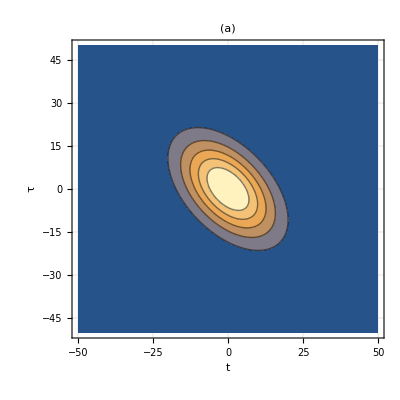

-Graphics-

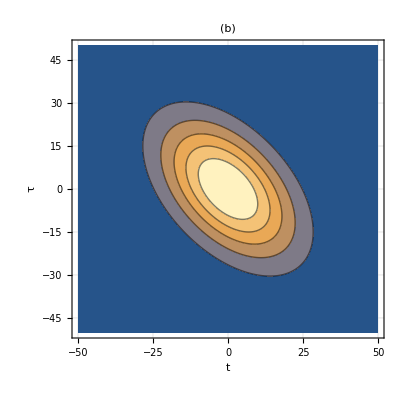

-Graphics-

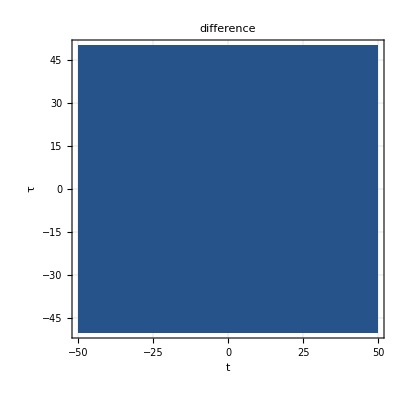

```mathematica
σF=0.1;
B1=10;
B2=20;
B3=30;
ContourPlot[
Exp[numer[σF,τ2,τ3,0,0,0,B1,B2,B3]/denom[σF,τ2,τ3,0,0,0,B1,B2,B3]],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},Axes->True,AxesStyle->Thick,PlotLabel->"(a)",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5
]
ContourPlot[
Exp[numer[σF,τ2,τ3,0,0,0,B1,-B2,-B3]/denom[σF,τ2,τ3,0,0,0,B1,-B2,-B3]],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},Axes->True,AxesStyle->Thick,PlotLabel->"(a)",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5
]
ContourPlot[
Classical[τ2,τ3,σF,B1,B2,B3],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},Axes->True,AxesStyle->Thick,PlotLabel->"(b)",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5
]
ContourPlot[
Classical[τ2,τ3,σF,B1,-B2,-B3],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},Axes->True,AxesStyle->Thick,PlotLabel->"(b)",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5
]
ContourPlot[
Exp[numer[σF,τ2,τ3,0,0,0,B1,B2,B3]/denom[σF,τ2,τ3,0,0,0,B1,B2,B3]]-Exp[numer[σF,τ2,τ3,0,0,0,B1,-B2,-B3]/denom[σF,τ2,τ3,0,0,0,B1,-B2,-B3]],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},Axes->True,AxesStyle->Thick,PlotLabel->"difference",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5
]
```

```mathematica
Manipulate[
GraphicsRow[{ContourPlot[
Exp[numer[σF,τ2,τ3,0,0,0,B1,B2,B3]/denom[σF,τ2,τ3,0,0,0,B1,B2,B3]],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->12,FontFamily->"Times", ,Black,Bold},Axes->True,AxesStyle->Thick,PlotLabel->"Quantum",ImageSize->Scaled[0.85],PlotRange->Full,Contours->5
],ContourPlot[
Classical[τ2,τ3,σF,B1,B2,B3],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->12,FontFamily->"Times", ,Black,Bold},Axes->True,AxesStyle->Thick,PlotLabel->"Classical",ImageSize->Scaled[0.85],PlotRange->Full,Contours->5
]}],
{σF,0.1,1,Appearance->{"Open"}},{B1,-50,50,Appearance->{"Open"}},{B2,-50,50,Appearance->{"Open"}},{B3,-50,50,Appearance->{"Open"}}]
```

## Cascaded

```mathematica
a=-ⅈ (B3+B4)+1/σF^2;
b=-ⅈ (τ-(A4-A3)+ω0/6 (B4-B3)+(B4-B3) ϵ);
c=0;
aprime=FullSimplify[Expand[-ⅈ (B1+(B3+B4)/4)+3/(4 σF^2)+(B4-B3)^2/(4a)],Element[ω0|A1|A3|A4|B1|B3|B4|t|τ|σF,Reals]];
bprime=FullSimplify[Expand[-ⅈ(t+τ/2+(A1-(A3+A4)/2)+(B1+(B3+B4)/4)ω0/3)+ω0/(4 σF^2)+((B4-B3)(τ-(A4-A3)+ω0/6(B4-B3)))/(4a)],Element[ω0|A1|A3|A4|B1|B3|B4|t|τ|σF,Reals]];
cprime=FullSimplify[Expand[1/(4a)(τ-(A4-A3)+ω0/6(B4-B3))^2-ⅈ((A1-(A3+A4)/2)ω0/6+ω0^2/36(B1+(B3+B4)/2))],Element[ω0|A1|A3|A4|B1|B3|B4|t|τ|σF,Reals]];

(*cprimeignored=ⅈ[(KF1+KF3+KF4)+ω0/12 τ+ω0/6 t+...];*)
n1=FullSimplify[Expand[bprime^2-4aprime cprime],Element[ω0|A1|A3|A4|B1|B3|B4|t|τ|σF,Reals]];
d1=FullSimplify[Expand[4 aprime],Element[ω0|A1|A3|A4|B1|B3|B4|t|τ|σF,Reals]];
```

```mathematica
n2=FullSimplify[Expand[n1 Conjugate [d1] + d1 Conjugate[n1]],Element[ω0|A1|A3|A4|B1|B3|B4|t|τ|σF,Reals]];
d2 = FullSimplify[d1 Conjugate[d1],Element[ω0|A1|A3|A4|B1|B3|B4|t|τ|σF,Reals]];
```

```mathematica
n3[σF_,B1_,B3_,B4_,ω0_,t_,τ_]:=1/(288 σF^6 (1+(B3+B4)^2 σF^4)^2)(576 t^2 σF^4 (-3-(7 B3^2+10 B3 B4+7 B4^2) σF^4-4 (B3+B4)^2 (B3^2+B3 B4+B4^2) σF^8)+108 ω0^2-192 t σF^4 (1+(B3+B4)^2 σF^4) (9 τ+6 (3 B3^2+B1 (B3-B4)+2 B3 B4+B4^2) σF^4 τ+(B3-B4)^2 (B1+B3+B4) σF^4 ω0)+24 σF^4 (-72 τ^2+9 (B3-B4) τ ω0+(8 B1^2+11 B3^2+16 B3 B4+11 B4^2+4 B1 (B3+B4)) ω0^2)+σF^8 (-36 (64 B1^2+105 B3^2+78 B3 B4+73 B4^2+16 B1 (3 B3+B4)) τ^2+12 (B3-B4) (32 B1^2+27 B3^2+10 B3 B4+43 B4^2+8 B1 (B3+3 B4)) τ ω0+(131 B3^4+564 B3^3 B4+722 B3^2 B4^2+564 B3 B4^3+131 B4^4+64 B1 (B3+B4) (B3^2+10 B3 B4+B4^2)+64 B1^2 (5 B3^2+14 B3 B4+5 B4^2)) ω0^2)+4 σF^12 (-36 (9 B3^4+21 B3^3 B4+28 B3^2 B4^2+5 B3 B4^3+B4^4+16 B1^2 (B3+B4)^2+2 B1 (B3+B4) (3 B3^2+14 B3 B4-B4^2)) τ^2+12 (B3-B4) (-3 B3^4-5 B3^3 B4+12 B3^2 B4^2+3 B3 B4^3+B4^4-4 B1 B3 (B3-5 B4) (B3+B4)+8 B1^2 (B3+B4)^2) τ ω0+(-B3^6+B3^5 B4+37 B3^4 B4^2+118 B3^3 B4^3+37 B3^2 B4^4+B3 B4^5-B4^6+32 B1^2 (B3+B4)^2 (B3^2+4 B3 B4+B4^2)-2 B1 (B3+B4) (B3^4-36 B3^3 B4-122 B3^2 B4^2-36 B3 B4^3+B4^4)) ω0^2));
d3[σF_,B1_,B3_,B4_,ω0_,t_,τ_]:=(9+8 (2 B1^2+2 B3^2+B3 B4+2 B4^2+B1 (B3+B4)) σF^4+16 (B3 B4+B1 (B3+B4))^2 σF^8)/(σF^4+(B3+B4)^2 σF^8);
```

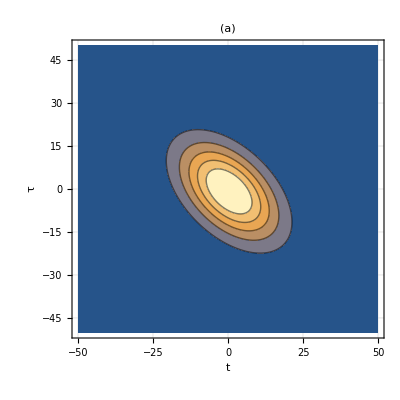

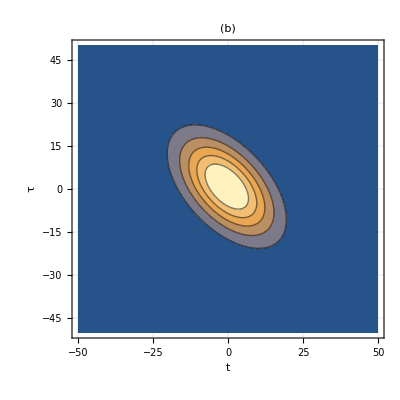

```mathematica
σF=0.1;
B1=20;
B2=20;
B3=30;
ω0=1;
ContourPlot[
Exp[n3[σF,B1,B2,B3,ω0,τ2,τ3]/d3[σF,B1,B2,B3,ω0,τ2,τ3]],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},Axes->True,AxesStyle->Thick,PlotLabel->"(a)",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5
]
ContourPlot[
Exp[n3[σF,B1,-B2,-B3,ω0,τ2,τ3]/d3[σF,B1,-B2,-B3,ω0,τ2,τ3]],{τ2,-50,50},{τ3,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},Axes->True,AxesStyle->Thick,PlotLabel->"(b)",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5
]
```

## Ignoring cross term in the integral

```mathematica
ClearAll[B1,B2,B3,σF]

a1=1/σF^2-ⅈ (B1+B3);
b1 =- ⅈ (t1-A1 -t3 + A3);
c1=0;
a2=1/σF^2-ⅈ (B2+B3);
b2 = -ⅈ (t2-A2 -t3 + A3);
c2=0;
t1=t0;
t2=t0+t;
t3=t0+t+τ;
term=FullSimplify[Expand[Expand[b1^2 b2^2 Conjugate[a1 a2]]+Expand[Conjugate[b1^2 b2^2]a1 a2]]/Expand[a1 a2 Conjugate[a1 a2]],Element[ω0|A1|A2|A3|B1|B2|B3|t0|t|τ|σF,Reals]]

term1[A1_,A2_,A3_]:=-(2 σF^4 (-1+(B1+B3) (B2+B3) σF^4) (A2-A3+τ)^2 (A1-A3+t+τ)^2)/(1+(B1^2+B2^2+2 B1 B3+2 B3 (B2+B3)) σF^4+(B1+B3)^2 (B2+B3)^2 σF^8);
term2 =term1[0,0,0]
```

-(2 σF^4 (-1+(B1+B3) (B2+B3) σF^4) (A2-A3+τ)^2 (A1-A3+t+τ)^2)/(1+(B1^2+B2^2+2 B1 B3+2 B3 (B2+B3)) σF^4+(B1+B3)^2 (B2+B3)^2 σF^8)

(2 σF^4 (-1+(B1+B3) (B2+B3) σF^4) τ^2 (t+τ)^2)/(1+(B1^2+B2^2+2 B1 B3+2 B3 (B2+B3)) σF^4+(B1+B3)^2 (B2+B3)^2 σF^8)

```mathematica
P[σF_,B1_,B2_,B3_,t_,τ_]:=Exp[-1/4(2 σF^4 (-1+(B1+B3) (B2+B3) σF^4) τ^2 (t+τ)^2)/(1+(B1^2+B2^2+2 B1 B3+2 B3 (B2+B3)) σF^4+(B1+B3)^2 (B2+B3)^2 σF^8)];
σF=0.1;
B1=10;
B2=-20;
B3=-30;
ContourPlot[
P[σF,B1,B2,B2,t,τ],{t,-50,50},{τ,-50,50},
PlotRange->Full,PlotRange->Full,PlotPoints->50,Mesh->None,AxesLabel->{"t","τ"},GridLines->Automatic,LabelStyle->{FontSize->60,FontFamily->"Times", Black},Axes->True,AxesStyle->Thick,PlotLabel->"Without cross terms",ImageSize->Scaled[0.5],PlotRange->Full,Contours->5,PlotLegends->Automatic
]
```

-Graphics-